```mathematica
gene = ""
```

MDM2

```mathematica
project = "AllProjects"
```

AllProjects

```mathematica
path = "/home/agarcia_pc/Programming_pc/Bioinformatica/ICGC/results/to-plot"
```

/home/agarcia_pc/Programming_pc/Bioinformatica/ICGC/results/to-plot

```mathematica
d = StringReplace[#, {"gene"-> gene, "project"-> project}]&
```

StringReplace[#1,{gene→gene,project→project}]&

```mathematica
f = StringReplace[#, {"gene"-> If[gene=="AllGenes", "", gene], "project"-> If[project=="AllProjects", "", project]}]&
```

StringReplace[#1,{gene→If[gene==AllGenes,,gene],project→If[project==AllProjects,,project]}]&

```mathematica
filename = StringReplace["path/file", {"path" -> path, "file" -> #}] &
```

StringReplace[path/file,{path→path,file→#1}]&

```mathematica
file = f["gene-project.plot.tsv"]
```

MDM2-.plot.tsv

```mathematica
plotName = d["Gene:gene & Project:project"]
```

Gene:MDM2 & Project:AllProjects

```mathematica
data = Import[filename[file]][[2;;]]
```

{{1,398},{2,26},{3,1},{5,1}}

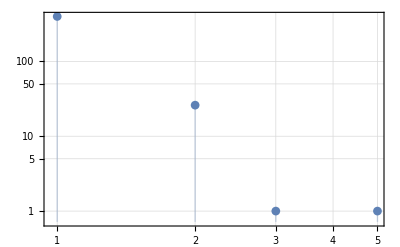

```mathematica
LogLogLegended =
ListLogLogPlot[data, PlotTheme->"Detailed", Joined -> False, PlotMarkers-> Automatic, Filling->Bottom, PlotLegends-> plotName]
(*LLLname = StringReplace["LogLog-PlotName-Legended.png", {"PlotName"-> "AllProjects&AllGenes"}]
Export[filename[LLLname], LogLogLegended]*)
```

```mathematica
data[[1]]
```

{1,398}

```mathematica
data[[45]]
```

Part::partw: Part 45 of {{1,398},{2,26},{3,1},{5,1}} does not exist.

{{1,398},{2,26},{3,1},{5,1}}⟦45⟧

```mathematica
fit = NonlinearModelFit[data[[;;]], A x^B,{A,B},x]
```

FittedModel[398.027/x^4.00414]

```mathematica
fit["BestFit"]
```

398.027/x^4.00414

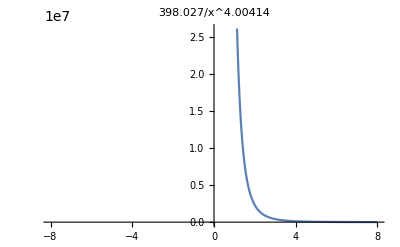

```mathematica
Plot[(4.36384641195045*^7)/x^4.252561332887292,{x,-8,8}, PlotLabel->fit["BestFit"]]
```

```mathematica
Normal[fit]
```

398.027/x^4.00414

```mathematica
fitString = StringReplace["y = A*x^B", {"A"->#1, "B"->#2}] &
```

StringReplace[y = A*x^B,{A→#1,B→#2}]&

```mathematica
fit["ParameterErrors"]
```

{2.89021,0.160509}

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 398.027 | 2.89021 | 137.716 | 0.0000527227
B | -4.00414 | 0.160509 | -24.9465 | 0.001603

```mathematica
fit["AdjustedRSquared"]
```

0.99979

```mathematica
fit["BestFitParameters"]
```

{A→398.027,B→-4.00414}

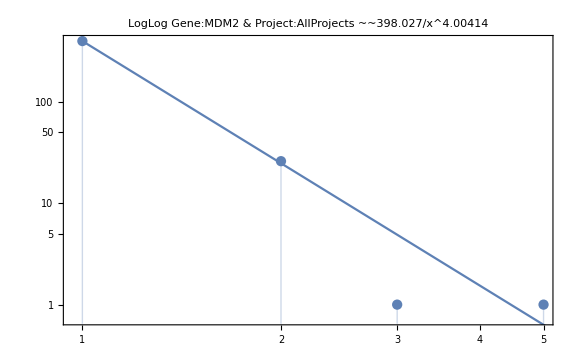

```mathematica
loglogFitPlot = Show[
ListLogLogPlot[data[[;;]], Filling -> Axis],
LogLogPlot[fit[x],{x,1,542}],
Frame->True,
ImageSize->Large,
PlotLabel -> StringReplace["LogLog PlotName Fit",{"PlotName"-> plotName, "Fit"-> fit["BestFit"]}]
]
```

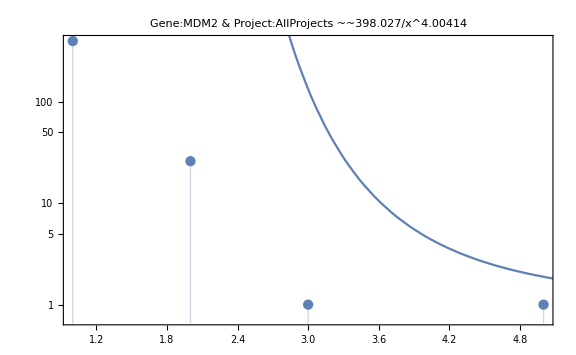

```mathematica
fitPlot = Show[
ListLogPlot[data[[;;]], Filling -> Axis],
Plot[fit[x],{x,0,14}],
Frame->True,
ImageSize -> Large,
PlotLabel -> StringReplace["PlotName Fit",{"PlotName"-> plotName, "Fit"-> fit["BestFit"]}]
]
```

```mathematica
fit["FitResiduals"]
```

{-0.0272049,1.19458,-3.89162,0.367386}

```mathematica
ListPlot[%206]
```

ListPlot::lpn: ATM-.plot.tsv is not a list of numbers or pairs of numbers.

ListPlot[ATM-.plot.tsv]

```mathematica
Total[%206]
```

Total::normal: Nonatomic expression expected at position 1 in Total[ATM-.plot.tsv].

Total[ATM-.plot.tsv]

```mathematica
Total[%194]
```

{}

```mathematica
Histogram[%103]
```

Histogram::ldata: Gene:TP53&Project: is not a valid dataset or list of datasets.

Histogram[Gene:TP53&Project:]

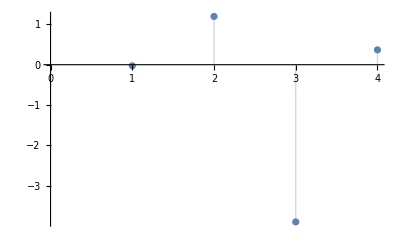

```mathematica
ListPlot[fit["FitResiduals"],Filling->Axis]
```

```mathematica
Remove[minimize]
```

```mathematica
minimize[data_, i0_] := 
Module[{i,fit,totalError, minValue = Infinity,min = i0, errors = {Nothing}},
For[i=min,i< Length[data], i = i+1, 
fit = NonlinearModelFit[data[[;;i]], A x^B,{A,B},x];
totalError = Abs[Total[fit["FitResiduals"]]];
errors = Append[errors, {i,totalError}];
If[totalError < minValue, min = i; minValue = totalError, Nothing];
Print[StringReplace["i:_i, error:_totalError, minimum:_minValue", {"_i"->i, "_totalError"->totalError, "_minValue"->minValue}]];
];
{min, errors}
]
```

```mathematica
m = minimize[data, 1]
```

i:~~1~~, error:~~0.~~, minimum:~~0.

i:~~2~~, error:~~7.21201×10^-13~~, minimum:~~0.

i:~~3~~, error:~~2.69958~~, minimum:~~0.

{1,{{1,0.},{2,7.21201×10^-13},{3,2.69958}}}

```mathematica
m
```

{1,{{1,0.},{2,7.21201×10^-13},{3,2.69958}}}

```mathematica
m[[2]]
```

{{1,0.},{2,7.21201×10^-13},{3,2.69958}}

```mathematica
TableForm[%180]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 1297. | 1.22955 | 1054.85 | 4.8994×10^-17
B | -4.72163 | 0.0350528 | -134.701 | 1.12904×10^-11

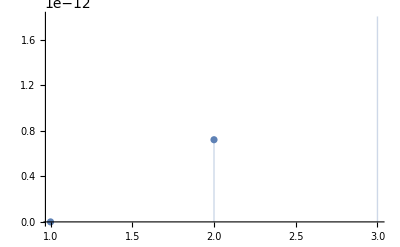

```mathematica
ListPlot[m[[2]],Joined->False, Filling->Axis]
```

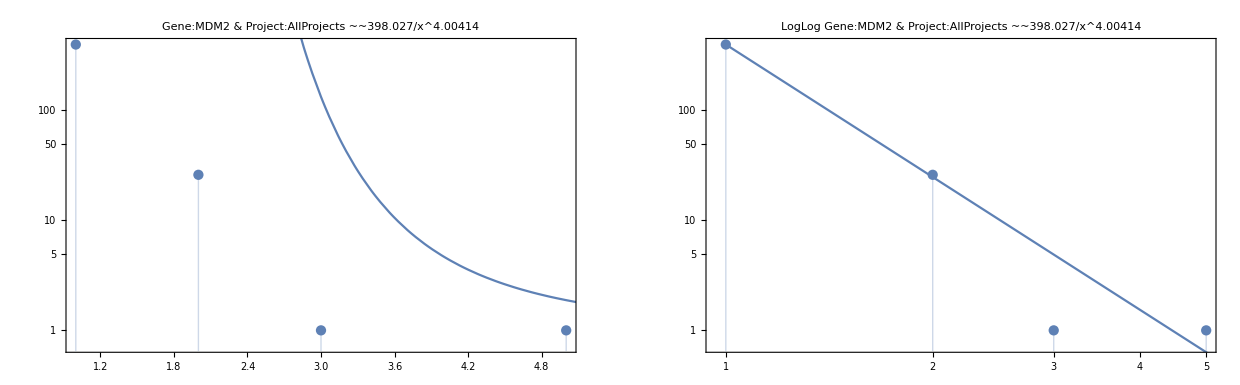

```mathematica
fitting = GraphicsGrid[{{fitPlot, loglogFitPlot}}]
```

```mathematica
Export[filename[d["fit-gene-project.png"]], fitting]
```

/home/agarcia_pc/Programming_pc/Bioinformatica/ICGC/results/to-plot/fit-MDM2-AllProjects.png